```mathematica
Needs["PlotLegends`"]
```

LegendPosition::shdw: Symbol "LegendPosition" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

```mathematica
dticks=Table[{(l-1)*90-180,ToString[(l-1)*90-180],{0,.01}},{l,1,5}]
fticks=Table[{l*1000,ToString[l*1000],{0,.01}},{l,1,7}]
```

{{-180,-180,{0,0.01}},{-90,-90,{0,0.01}},{0,0,{0,0.01}},{90,90,{0,0.01}},{180,180,{0,0.01}}}

{{1000,1000,{0,0.01}},{2000,2000,{0,0.01}},{3000,3000,{0,0.01}},{4000,4000,{0,0.01}},{5000,5000,{0,0.01}},{6000,6000,{0,0.01}},{7000,7000,{0,0.01}}}

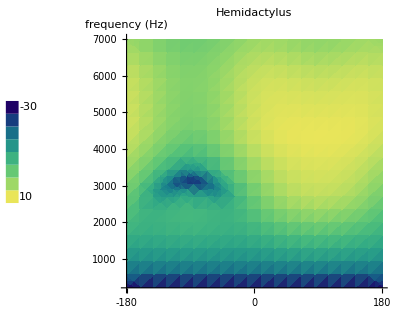

```mathematica
ShowLegend[DensityPlot[20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)],{θ,-180,180},{f,200,7000},ColorFunction->"BlueGreenYellow",PlotPoints->20,Frame->False,Axes->True,AxesOrigin->{-180,200},AxesLabel->{None,"frequency (Hz)"},Ticks->{dticks,fticks},PlotLabel->"Hemidactylus",FrameLabel->{"direction(degrees)",None}],{ColorData["BlueGreenYellow"][#1]&,8,"-30","10",LegendPosition->{-1.5,-.35},LegendOrientation->Vertical}]
```

```mathematica
dbticks=Table[{(l-1)*10-40,ToString[(l-1)*10-40],{0,.005}},{l,1,6}]
fticks2=Table[{l*1000,ToString[l],{0,.005}},{l,1,5}]
```

{{-40,-40,{0,0.005}},{-30,-30,{0,0.005}},{-20,-20,{0,0.005}},{-10,-10,{0,0.005}},{0,0,{0,0.005}},{10,10,{0,0.005}}}

{{1000,1,{0,0.005}},{2000,2,{0,0.005}},{3000,3,{0,0.005}},{4000,4,{0,0.005}},{5000,5,{0,0.005}}}

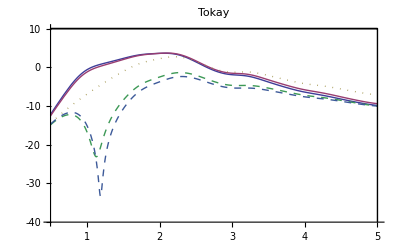

```mathematica
Plot[{20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->90,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->60,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->0,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->-60,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->-90},{f,500,5000},PlotRange->{-40,10},PlotStyle->{ColorData[1][1],ColorData[1][2],Dotted,Dashed,Dashed},AxesOrigin->{500,-40},PlotLabel->"Tokay",Epilog->{Line[{{5000,-40},{5000,10},{500,10},{5000,10}}]},Ticks->{fticks2,dbticks},PlotLegend->{"90°","60°","0°","-60°","-90°"},LegendPosition->{.9,-.4}]
```

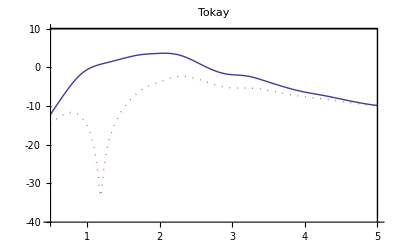

```mathematica
Plot[{20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->90,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->-90},{f,500,5000},PlotRange->{-40,10},PlotStyle->{ColorData[1][1],Dotted},AxesOrigin->{500,-40},PlotLabel->"Tokay",Epilog->{Line[{{5000,-40},{5000,10},{500,10},{5000,10}}]},Ticks->{fticks2,dbticks},PlotLegend->{"90°","-90°"},LegendPosition->{.9,-.3}]
```

```mathematica
dticks=Table[{(l-1)*90-180,ToString[(l-1)*90-180],{0,.01}},{l,1,5}]
dbticks=Table[{(l-1)*10-20,ToString[(l-1)*10-20],{0,.005}},{l,1,3}]
```

{{-180,-180,{0,0.01}},{-90,-90,{0,0.01}},{0,0,{0,0.01}},{90,90,{0,0.01}},{180,180,{0,0.01}}}

{{-20,-20,{0,0.005}},{-10,-10,{0,0.005}},{0,0,{0,0.005}}}

{{-180,-180,{0,0.01}},{-90,-90,{0,0.01}},{0,0,{0,0.01}},{90,90,{0,0.01}},{180,180,{0,0.01}}}

{{500,500,{0,0.01}},{1000,1000,{0,0.01}},{1500,1500,{0,0.01}},{2000,2000,{0,0.01}},{2500,2500,{0,0.01}},{3000,3000,{0,0.01}},{3500,3500,{0,0.01}}}

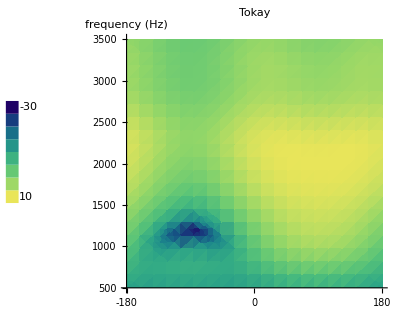

```mathematica
dticks=Table[{(l-1)*90-180,ToString[(l-1)*90-180],{0,.01}},{l,1,5}]
fticks=Table[{l*500,ToString[l*500],{0,.01}},{l,1,7}]
ShowLegend[DensityPlot[20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)],{θ,-180,180},{f,
500,3500},ColorFunction->"BlueGreenYellow",PlotPoints->20,PlotRange->35,Frame->False,Axes->True,AxesOrigin->{-180,500},AxesLabel->{None,"frequency (Hz)"},Ticks->{dticks,fticks},PlotLabel->"Tokay",FrameLabel->{"direction(degrees)",None}],{ColorData["BlueGreenYellow"][#1]&,8,"-30","10",LegendPosition->{-1.5,-.35},LegendOrientation->Vertical}]
```

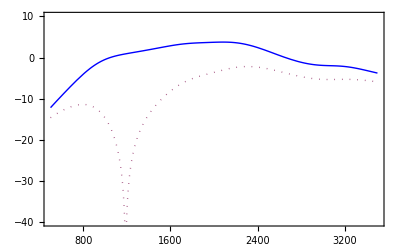

```mathematica
Plot[{20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->90,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->-90},{f,500,3500},Frame->True,Axes->False,PlotRange->{-40,10},PlotStyle->{Blue,Dotted}]
```

```mathematica
ColorData[1][1]
```

RGBColor[0.2472,0.24,0.6]

```mathematica
dticks=Table[{(l-1)*90-180,ToString[(l-1)*90-180],{0,.01}},{l,1,5}]
dbticks=Table[{(l-1)*5-5,ToString[(l-1)*5-5],{0,.005}},{l,1,3}]
```

{{-180,-180,{0,0.01}},{-90,-90,{0,0.01}},{0,0,{0,0.01}},{90,90,{0,0.01}},{180,180,{0,0.01}}}

{{-5,-5,{0,0.005}},{0,0,{0,0.005}},{5,5,{0,0.005}}}

7.5

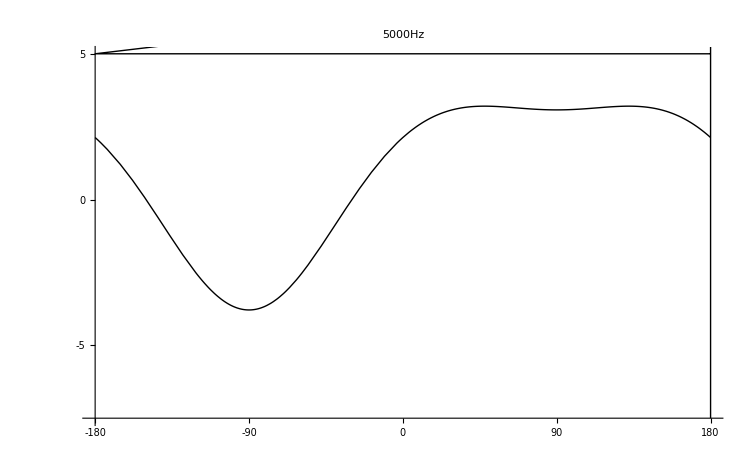

```mathematica
prange=7.5
Plot[20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.f->5000,{θ,-180,180},PlotRange->{-prange,5},PlotStyle->Black,AxesOrigin->{-180,-prange},PlotLabel->"5000Hz",Ticks->{dticks,dbticks},Epilog->{Line[{{180,-prange},{180,prange},{-180,5},{180,5}}]}]
```

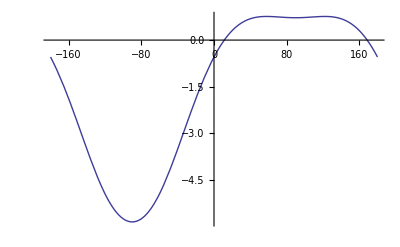

```mathematica
Plot[20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.f->5000,{θ,-180,180}]
```

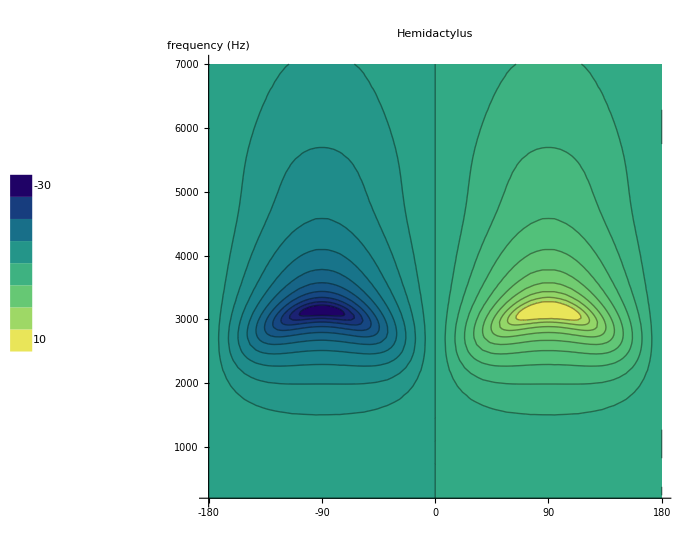

```mathematica
ShowLegend[ContourPlot[20*Log10[Abs[SL/S0]],{θ,-180,180},{f,200,7000},ColorFunction->"BlueGreenYellow",PlotPoints->20,Contours->20,Frame->False,Axes->True,AxesOrigin->{-180,200},AxesLabel->{None,"frequency (Hz)"},Ticks->{dticks,fticks},PlotLabel->"Hemidactylus",FrameLabel->{"direction(degrees)",None}],{ColorData["BlueGreenYellow"][#1]&,8,"-30","10",LegendPosition->{-1.5,-.35},LegendOrientation->Vertical}]
```

{{-180,-180,{0,0.01}},{-90,-90,{0,0.01}},{0,0,{0,0.01}},{90,90,{0,0.01}},{180,180,{0,0.01}}}

{{500,500,{0,0.01}},{1000,1000,{0,0.01}},{1500,1500,{0,0.01}},{2000,2000,{0,0.01}},{2500,2500,{0,0.01}},{3000,3000,{0,0.01}},{3500,3500,{0,0.01}}}

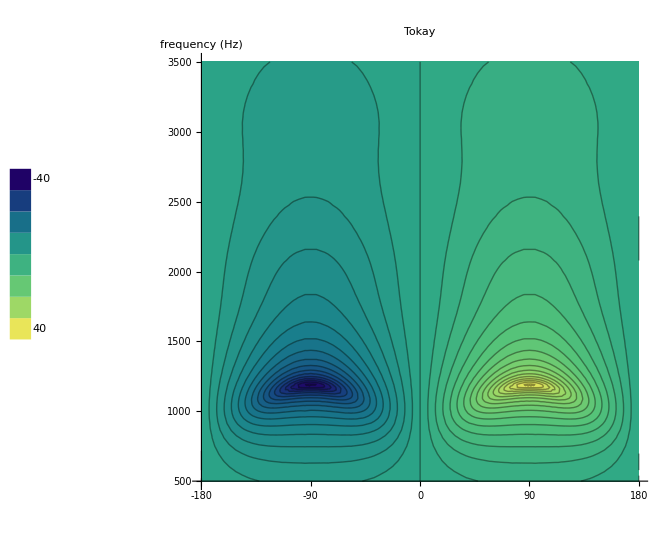

```mathematica
dticks=Table[{(l-1)*90-180,ToString[(l-1)*90-180],{0,.01}},{l,1,5}]
fticks=Table[{l*500,ToString[l*500],{0,.01}},{l,1,7}]
ShowLegend[ContourPlot[20*Log10[Abs[SL/S0]],{θ,-180,180},{f,
500,3500},ColorFunction->"BlueGreenYellow",PlotPoints->20,Contours->40,PlotRange->45,Frame->False,Axes->True,AxesOrigin->{-180,500},AxesLabel->{None,"frequency (Hz)"},Ticks->{dticks,fticks},PlotLabel->"Tokay",FrameLabel->{"direction(degrees)",None}],{ColorData["BlueGreenYellow"][#1]&,8,"-40","40",LegendPosition->{-1.5,-.35},LegendOrientation->Vertical}]
```

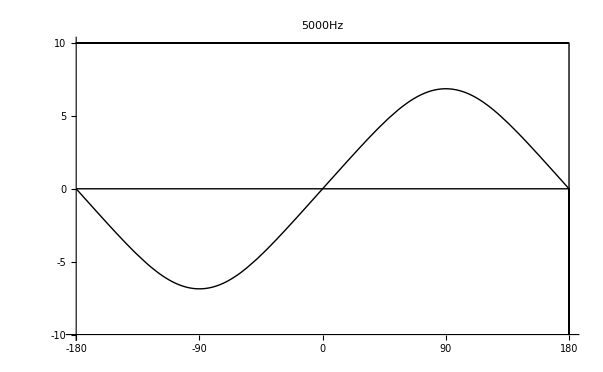

```mathematica
Plot[20*Log10[Abs[SL/S0]]/.f->5000,{θ,-180,180},PlotRange->10,PlotStyle->Black,AxesOrigin->{-180,-10},PlotLabel->"5000Hz",Ticks->{dticks,dbticks},Epilog->{Line[{{-180,0},{180,0},{180,-10},{180,10},{-180,10},{180,10}}]}]
```

```mathematica
_□
```

```mathematica
dticks=Table[{(l-1)*90-180,ToString[(l-1)*90-180],{0,.01}},{l,1,5}]
dbticks=Table[{(l-1)*5-10,ToString[(l-1)*5-10],{0,.005}},{l,1,5}]
```

{{-180,-180,{0,0.01}},{-90,-90,{0,0.01}},{0,0,{0,0.01}},{90,90,{0,0.01}},{180,180,{0,0.01}}}

{{-10,-10,{0,0.005}},{-5,-5,{0,0.005}},{0,0,{0,0.005}},{5,5,{0,0.005}},{10,10,{0,0.005}}}

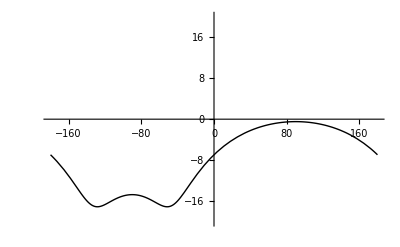

```mathematica
Plot[20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.f->1000,{θ,-180,180},PlotRange->{-20,20},PlotStyle->Black]
```

```mathematica
dbticks=Table[{(l-1)*10-40,ToString[(l-1)*10-40],{0,.005}},{l,1,6}]
fticks2=Table[{l*1000,ToString[l],{0,.005}},{l,1,7}]
```

{{-40,-40,{0,0.005}},{-30,-30,{0,0.005}},{-20,-20,{0,0.005}},{-10,-10,{0,0.005}},{0,0,{0,0.005}},{10,10,{0,0.005}}}

{{1000,1,{0,0.005}},{2000,2,{0,0.005}},{3000,3,{0,0.005}},{4000,4,{0,0.005}},{5000,5,{0,0.005}},{6000,6,{0,0.005}},{7000,7,{0,0.005}}}

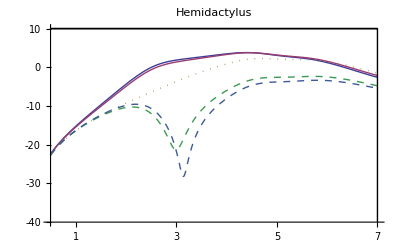

```mathematica
Plot[{20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->90,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->60,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->0,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->-60,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->-90},{f,500,7000},PlotRange->{-40,10},PlotStyle->{ColorData[1][1],ColorData[1][2],Dotted,Dashed,Dashed},AxesOrigin->{500,-40},PlotLabel->"Hemidactylus",Epilog->{Line[{{7000,-40},{7000,10},{500,10},{7000,10}}]},Ticks->{fticks2,dbticks},PlotLegend->{Style["90°",18],Style["60°",18],Style["0°",18],Style["-60°",18],Style["-90°",18]},LegendPosition->{.9,-.4}]
```

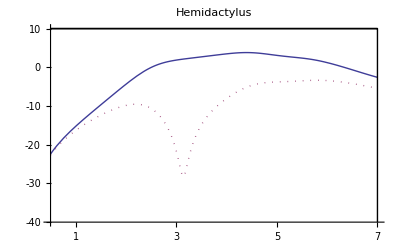

```mathematica
Plot[{20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->90,20*Log10[ω*Abs[SL]/(Pi*acyl*acyl)]/.θ->-90},{f,500,7000},PlotRange->{-40,10},PlotStyle->{ColorData[1][1],Dotted},AxesOrigin->{500,-40},PlotLabel->"Hemidactylus",Epilog->{Line[{{7000,-40},{7000,10},{500,10},{7000,10}}]},Ticks->{fticks2,dbticks},PlotLegend->{Style["90°",18],Style["-90°",18]},LegendPosition->{.9,-.3}]
```